Your Title Here

```mathematica
colL=Blue;colV=RGBColor[0,0.6,0];
```

```mathematica
text[var_,sub_]:=Framed[Style[Subscript[Style[var,Italic],sub],17],Background->White,FrameStyle->None,FrameMargins->Tiny];
```

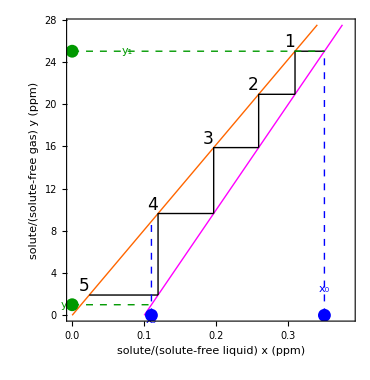





```mathematica
Module[{yN1,x0,xN,T,P,LVmax,Ea,R,T0,H0,H,yeq,L,V,yop,xmin1,xmin2,ymin,y1,xop,check,X,Y,ntest,n},
yN1=1;x0=0.35;xN=0.11;T=13;P=2.4;LVmax=False;

Ea=5000;R=8.314;T0=298;H0=211.19;(*atm/mole frac.*)
H=H0*Exp[-Ea/R*(1/(T+273)-1/T0)];
yeq[x_]:=H/P*x;

L=100;V=1;
yop[x_]:=L/V*(x-x0)+y1;

xmin1=x/.Solve[yop[x]==0,x][[1]];
xmin2=x/.Solve[yeq[x]==1.1*y1,x][[1]];
ymin[x_]:=(yeq[xmin2]-0)/(xmin2-xmin1)*(x-xmin1);

(*y1=yN1-L/V*(xN-x0);*)
y1=y/.Solve[x0*L+yN1*V==xN*L+y*V,y][[1]];
xop=1.1*x0;

check=x/.Solve[yeq[x]==yop[x],x][[1]];

X[0]=x0;Y[0]=yop[x0];
Do[{X[i]=x/.Solve[yeq[x]==Y[i-1],x,Reals][[1]],Y[i]=yop[X[i]]},{i,1,75}];
ntest=1+DeleteCases[If[X[#]<xN,0,#]&/@Range@50,0];
n=If[Length@ntest==0,0,ntest[[-1]]];


Plot[{yop[x],yeq[x]},{x,0,xop},PlotStyle->{{Thick,If[LVmax∧(yeq[xop]>yop[xop])∧(yop[0]<yeq[0]),Transparent,Magenta]},{Thick,RGBColor[1,0.4,0]}},PlotRange->{0,1.1*y1},PlotRangePadding->None,PlotRangeClipping->False,
Frame->True,FrameLabel->{Row@{"solute/(solute-free liquid) ",Style["x",Italic], " (ppm)"},Row@{"solute/(solute-free gas) ",Style["y",Italic]," (ppm)"}},LabelStyle->{17,Black},ImageSize->{370,380},AspectRatio->Full,
Epilog->{Thick,PointSize@0.025,
If[LVmax==False∧(check<0∨check>xop)∧(yeq[xop]>yop[xop])∧n≠0,{
(*STAGES*)
If[(check<0∨check>xop)∧n≠0,{Line[{{X[#-1],Y[#-1]},{X[#],Y[#-1]},{X[#],Y[#]}}]&/@Range[n-1],Line[{{X[n-1],Y[n-1]},{X[n],Y[n-1]}(*,{X[n],yN1}*)}]}],
(*yN+1 LINE*)
{Dashed,colV,Line[{{0,yN1},{xN,yN1}}],Text[text["y",n+1],{0,yN1},{1.2,0}],Point@{0,yN1}},
(*x0 AND y1 LINES*)
{Dashed,colL,Line[{{x0,0},{x0,yop[x0]}}],Text[text["x",0],{x0,2.5}],Point@{x0,0}},
{Dashed,colV,Line[{{0,y1},{x0,y1}}],Text[text["y",1],{0.2*xop,y1}],Point@{0,y1}},
(*xN LINE*)
{Dashed,colL,Line[{{xN,0},{xN,yeq[xN]}}],Text[text["x",n],{xN,0},{0,1.2}],Point@{xN,0}},
(*STAGES*)
If[check<0∨check>xop,{
(*If[n≤12,{Text[Style[#,17,Background->White],{X[#-1],Y[#-1]},{-1.2,1}]&/@Range@n}],*)
If[n≤12,{Text[Style[#,17,Background->White],{X[#],Y[#-1]},{1.2,-1}]&/@Range@n}],
If[n>12,{Text[Style[n,17,Background->White],{X[n],Y[n-1]},{1.2,-1}],Text[Style[1,17,Background->White],{X[0],Y[0]},{1.2,-1}]}]}],


(*(*INLET AND OUTLET STAGE BALANCES*)
Text[Style[Column[{Row@{"stage ",tray," solute fluxes:"},Column[{
Row@{"in: ",NumberForm[X[(*n+1-*)tray]*L+yop[X[(*n+1-*)tray-1]]*V,{4,0}]," mol/h"},
Row@{"out: ",NumberForm[X[(*n+1-*)tray-1]*L+yop[X[(*n+1-*)tray]]*V,{4,0}]," mol/h"}
},Alignment->":"]},Center],17],{0.105,20}]*)
}],
(*separation not possible*)
If[(0≤check≤xop)∨yeq[xop]<yop[xop],Text[Framed[Column[{Style["separation not possible",20,RGBColor[0.85,0,0]],Style["⋆infinite stages needed⋆",17]},Center],Background->White],{0.5*xop,0.5*y1}]],
If[n==0,Text[Framed[Style["separation not possible",20,RGBColor[0.85,0,0]],Background->White],{0.5*xop,0.5*y1}]],
(*L/V min*)
If[LVmax∧(yeq[xop]>yop[xop])∧(yop[0]<yeq[0]),{Magenta,Line[{{xmin1,ymin[xmin1]},{xmin2,ymin[xmin2]}}]}],
(*OPERATING AND EQUILIBRIUM LINE LABELS*)
}]
]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX